Finding Clusters in Text
Ian Milligan - 23 August 2016

```mathematica
enchantedfiles=Import["/users/ianmilligan1/dropbox/GeoCities-data/1000-enchantedforest.txt","Lines"];
```

```mathematica
res=FindClusters[enchantedfiles,10];
```

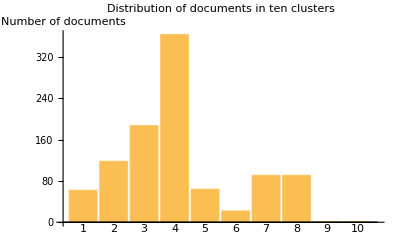

```mathematica
BarChart[Length[res⟦#⟧]&/@Range[10],AxesLabel->"Number of documents",PlotLabel->"Distribution of documents in ten clusters",ChartLabels->Range[10]]
```

```mathematica
TableForm[res⟦1⟧]
```

(20090723,geocities.com,http://geocities.com/EnchantedForest/1002/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:31 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/gladys2.geo/index.html X-INKT-SITE: http://us.geocities.com/gladys2.geo Last-Modified: Fri, 03 Dec 2004 06:46:27 GMT Accept-Ranges: bytes Content-Length: 14942 Cache-Control: private Connection: close Content-Type: text/html Histoires Ã  raconter ou lire)
(20090723,geocities.com,http://geocities.com/EnchantedForest/1833/MAGEPAGE.HTM,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:33 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/ljkaiser_1823/MAGEPAGE.HTM X-INKT-SITE: http://us.geocities.com/ljkaiser_1823 Last-Modified: Thu, 18 Apr 2002 02:21:51 GMT Accept-Ranges: bytes Content-Length: 1657 Cache-Control: private Connection: close Content-Type: text/html MAGEPAGE Â  Thanks for joining us here at Michigan Alliance for Gifted Education. Our web site name has changed. Â  Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/2125/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:38 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/smcards.geo/index.html X-INKT-SITE: http://us.geocities.com/smcards.geo Last-Modified: Wed, 19 Aug 1998 21:16:00 GMT Accept-Ranges: bytes Content-Length: 1795 Cache-Control: private Connection: close Content-Type: text/html You are Seiya/Starfighter fan # to enter the shrine since June 1st, 1998 at 10:00pm PST.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/2175/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:38 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w6.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/ickapus/index.html X-INKT-SITE: http://us.geocities.com/ickapus Last-Modified: Tue, 17 Feb 2004 05:22:53 GMT Accept-Ranges: bytes Content-Length: 5126 Cache-Control: private Connection: close Content-Type: text/html Some other interesting sites:)
(20090723,geocities.com,http://geocities.com/EnchantedForest/2292/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:41 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/hiscastle/index.html X-INKT-SITE: http://us.geocities.com/hiscastle Last-Modified: Thu, 08 Jul 1999 22:37:33 GMT Accept-Ranges: bytes Content-Length: 6263 Cache-Control: private Connection: close Content-Type: text/html Historia's Castle Handouts for)
(20090723,geocities.com,http://geocities.com/EnchantedForest/4364/pd.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:43 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/twilightmlp/pd.html X-INKT-SITE: http://us.geocities.com/twilightmlp Last-Modified: Sun, 01 Dec 2002 01:53:38 GMT Accept-Ranges: bytes Content-Length: 2372 Cache-Control: private Connection: close Content-Type: text/html Instructions Choose a pony Draw a symbol and color her and her clothes Cut her and her clothes out Take her out on an adventure!)
(20090723,geocities.com,http://geocities.com/EnchantedForest/8989/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:22 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/nestoncivic/index.html X-INKT-SITE: http://us.geocities.com/nestoncivic Last-Modified: Tue, 14 Nov 2000 00:32:08 GMT Accept-Ranges: bytes Content-Length: 6253 Cache-Control: private Connection: close Content-Type: text/html Neston is an important historic town which has been occupied since Saxon times.Â  A town of warm sandstone and mellow brick, with many fine historic buildings.Â  It is a beautiful place to live, work and visit. NESTON CIVIC SOCIETY Is registered with The Civic Trust and the Charities Commission No: 515628)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Cottage/2496/,ï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bd)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/1006/lego.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:51 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/dnjhess/lego.html X-INKT-SITE: http://us.geocities.com/dnjhess Last-Modified: Thu, 10 Apr 2008 00:33:51 GMT Accept-Ranges: bytes Content-Length: 2228 Cache-Control: private Connection: close Content-Type: text/html My photos have moved to Flickr .)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/8343/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:34 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w1.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/cargass.geo/index.html X-INKT-SITE: http://us.geocities.com/cargass.geo Last-Modified: Fri, 16 Jan 1998 23:39:51 GMT Accept-Ranges: bytes Content-Length: 2120 Cache-Control: private Connection: close Content-Type: text/html cargass 's Home Page This page hosted by)
(20090723,geocities.com,http://geocities.com/EnchantedForest/2755/kantoj.html,HTTP/1.1 503 Service Temporarily Unavailable Date: Thu, 23 Jul 2009 05:45:42 GMT Cache-Control: private Connection: close Content-Type: text/html; charset=iso-8859-1 Sorry, Service Temporarily Unavailable. The server is temporarily unable to service your request due to maintenance downtime or capacity problems. Please try again later. Additionally, a 503 Service Temporarily Unavailable error was encountered while trying to use an ErrorDocument to handle the request. Please check the URL for proper spelling and capitalization. If you're having trouble locating a destination on Yahoo!, try visiting the Yahoo! home page or look through a list of Yahoo!'s online services . Also, you may find what you're looking for if you try searching below. Search the Web Please try Yahoo! Help Central if you need more assistance.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/1130/pandb.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:32 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/snowfire_.geo/pandb.html X-INKT-SITE: http://us.geocities.com/snowfire_.geo Expires: Wed, 22 Jul 2009 05:45:32 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:45:32 GMT Cache-Control: private Connection: close Content-Type: text/html Pinky and the Brain ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd)
(20090723,geocities.com,http://geocities.com/EnchantedForest/3407/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:42 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/17thhw.geo/index.html X-INKT-SITE: http://us.geocities.com/17thhw.geo Last-Modified: Mon, 08 Jun 1998 23:21:57 GMT Accept-Ranges: bytes Content-Length: 3658 Cache-Control: private Connection: close Content-Type: text/html 17th HUMBER WEST SCOUT GROUP Our Provence Learn more about the Province we live in. Secsions Learn more about each Section. Leader Who are the Leaders in each Section? Cub's Survey PLease take a moment to fill out our Cubs Survey. You are Visitor Number)
(20090723,geocities.com,http://geocities.com/EnchantedForest/6157/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:59 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/laspina.geo/index.html X-INKT-SITE: http://us.geocities.com/laspina.geo Last-Modified: Mon, 04 Mar 2002 12:45:04 GMT Accept-Ranges: bytes Content-Length: 1957 Cache-Control: private Connection: close Content-Type: text/html La pagina di Marcello La Spina Le religioni sono come le lucciole, hanno bisogno dell'oscuritï¿.bd per brillare (Schopenauer) Scacchi This page hosted by)
(20090723,geocities.com,http://geocities.com/EnchantedForest/8036/allaboutus.html,HTTP/1.1 503 Service Temporarily Unavailable Date: Thu, 23 Jul 2009 05:46:19 GMT Cache-Control: private Connection: close Content-Type: text/html; charset=iso-8859-1 Sorry, Service Temporarily Unavailable. The server is temporarily unable to service your request due to maintenance downtime or capacity problems. Please try again later. Additionally, a 503 Service Temporarily Unavailable error was encountered while trying to use an ErrorDocument to handle the request. Please check the URL for proper spelling and capitalization. If you're having trouble locating a destination on Yahoo!, try visiting the Yahoo! home page or look through a list of Yahoo!'s online services . Also, you may find what you're looking for if you try searching below. Search the Web Please try Yahoo! Help Central if you need more assistance.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Cottage/1615/raggedy.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:34 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w1.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/grammy_girl/raggedy.html X-INKT-SITE: http://us.geocities.com/grammy_girl Expires: Wed, 22 Jul 2009 05:46:34 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:46:34 GMT Cache-Control: private Connection: close Content-Type: text/html these banners do not reflect my personal preferences or endorsements WELCOME TO RAGGEDY ANN'S GRAPHICS Adapted from original artwork of Johnny Gruelle, ca. 1920)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/6934/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:56 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w1.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/adam_12.geo/index.html X-INKT-SITE: http://us.geocities.com/adam_12.geo Last-Modified: Thu, 20 Jan 2000 20:49:48 GMT Accept-Ranges: bytes Content-Length: 12760 Cache-Control: private Connection: close Content-Type: text/html Updated 1/20/00 Starcraft Hero's United Earth Directorates Military Warning:)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Glade/5657/hallo1.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:57 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/woody93.geo/hallo1.html X-INKT-SITE: http://us.geocities.com/woody93.geo Last-Modified: Fri, 21 Sep 2001 20:39:57 GMT Accept-Ranges: bytes Content-Length: 2561 Cache-Control: private Connection: close Content-Type: text/html If this page does not auto redirect to the main page please click HERE . Thank you. You are brave soul number to make it this far!)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Meadow/1024/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:48:05 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/cratercreatures/index.html X-INKT-SITE: http://us.geocities.com/cratercreatures Last-Modified: Thu, 22 Jul 2004 04:16:20 GMT Accept-Ranges: bytes Content-Length: 1653 Cache-Control: private Connection: close Content-Type: text/html Welcome to)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Mountain/6559/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:48:48 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/cubpack152/index.html X-INKT-SITE: http://us.geocities.com/cubpack152 Last-Modified: Thu, 28 Sep 2000 03:13:40 GMT Accept-Ranges: bytes Content-Length: 5612 Cache-Control: private Connection: close Content-Type: text/html Welcome to the Home of Cub Scout Pack 152 Â  Â  Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Pond/2571/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:49:19 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/emmasgalaxy/index.htm X-INKT-SITE: http://us.geocities.com/emmasgalaxy Last-Modified: Fri, 22 Oct 1999 19:09:24 GMT Accept-Ranges: bytes Content-Length: 1842 Cache-Control: private Connection: close Content-Type: text/html Hiya! I'm Emma. I'm 10 years old. I live with my mom and dad and I have two sisters. Some things that I really like are  karate, sparring, fencing, trumpet, playing on the computer and reading. Come and check out my site!)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Pond/4130/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:49:22 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w2.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/parchis79/index.html X-INKT-SITE: http://us.geocities.com/parchis79 Last-Modified: Sun, 08 Feb 2004 18:48:45 GMT Accept-Ranges: bytes Content-Length: 3522 Cache-Control: private Connection: close Content-Type: text/html BIENVENIDO A: Â  Â  Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/2292/Meso/quiz4a.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:42 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w2.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/hiscastle/Meso/quiz4a.html X-INKT-SITE: http://us.geocities.com/hiscastle Last-Modified: Wed, 19 May 1999 18:03:16 GMT Accept-Ranges: bytes Content-Length: 5501 Cache-Control: private Connection: close Content-Type: text/html Allow time for the quiz to load. Read each question carefully. Return to the Castle BookMarks for Futher Consideration)
(20090723,geocities.com,http://geocities.com/EnchantedForest/2292/index.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:42 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/hiscastle/index.html X-INKT-SITE: http://us.geocities.com/hiscastle Last-Modified: Thu, 08 Jul 1999 22:37:33 GMT Accept-Ranges: bytes Content-Length: 6263 Cache-Control: private Connection: close Content-Type: text/html Historia's Castle Handouts for)
(20090723,geocities.com,http://geocities.com/EnchantedForest/8314/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:19 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/gobulldogs.geo/index.html X-INKT-SITE: http://us.geocities.com/gobulldogs.geo Last-Modified: Sat, 16 Aug 2003 17:23:35 GMT Accept-Ranges: bytes Content-Length: 2889 Cache-Control: private Connection: close Content-Type: text/html 4991 Southside Road Hollister, CA 95023)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Cottage/1184/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:31 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/snow_white_grumpy/index.html X-INKT-SITE: http://us.geocities.com/snow_white_grumpy Last-Modified: Tue, 19 Oct 1999 19:10:49 GMT Accept-Ranges: bytes Content-Length: 4052 Cache-Control: private Connection: close Content-Type: text/html Snow White's Cottage Welcome to My Website!  Click on a link above to visit the areas of my website.  Have fun exploring My page dedicated to Disney's Snow White and the Seven Dwarfs. This page hosted by)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/2038/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:51 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/r1gger1/index.htm X-INKT-SITE: http://us.geocities.com/r1gger1 Last-Modified: Sun, 19 Mar 2006 23:58:45 GMT Accept-Ranges: bytes Content-Length: 11953 Cache-Control: private Connection: close Content-Type: text/html The Bartenope Family Gulf Coast Edition Â  Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â  Â Photo Â© Photo Disc, Inc.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/5476/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:56 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w6.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/troop2493/index.html X-INKT-SITE: http://us.geocities.com/troop2493 Last-Modified: Tue, 16 Dec 2003 13:50:25 GMT Accept-Ranges: bytes Content-Length: 11262 Cache-Control: private Connection: close Content-Type: text/html Junior Girl Scout Troop 2493 The girls are on their way to earning their Silver Award.Â  Check out out Whats Happening page to see what they've been up to so far this year. Please take the time to sign ourÂ  guestbook , or send us an email .Â  we'd love to hear from you.Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/1420/main.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:08 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/sub-zero321/main.html X-INKT-SITE: http://us.geocities.com/sub-zero321 Expires: Wed, 22 Jul 2009 05:47:08 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:47:08 GMT Cache-Control: private Connection: close Content-Type: text/html Cheat Vault 2K Welcome to the Cheat Vault 2K. You are the _____________________________________________________________________________ Free JavaScripts provided ----------------------------------------------------------------------------)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/7012/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:17 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/tnsgmfan/index.html X-INKT-SITE: http://us.geocities.com/tnsgmfan Last-Modified: Fri, 21 Nov 2003 19:46:35 GMT Accept-Ranges: bytes Content-Length: 3292 Cache-Control: private Connection: close Content-Type: text/html In Memoriam ofÂ  Â Â Â Â Â Â Â Â Â  Â Â Â Â Â Â Â Â Â Â  Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â  "There is a destiny that makes us brothers, None goes his way alone;       All that we send into the lives of others, Comes back into our       own."Â -- Mary Stuart You are visitor #Â  Â  Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/7379/wishbone.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:25 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/sunnymack.geo/wishbone.html X-INKT-SITE: http://us.geocities.com/sunnymack.geo Last-Modified: Mon, 02 Aug 1999 00:09:52 GMT Accept-Ranges: bytes Content-Length: 2566 Cache-Control: private Connection: close Content-Type: text/html The Squeekee Book However, all the the links are still fully functional.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Glade/5207/,Â  Â  Besides                  us you will see other cute babies at the Cute Babies                  Club ...                  Ibu (mommy) used to pick the cutest baby each month.. she'll try to do that again BUT... she can't promise anything... We                  live in Jakarta Indonesia, Ibu asked us if she can use our homepage for info on and of course we said it's ok...... as long as... she updates our info and pictures frequently... But                  she also has a complete site in Indonesian about                  moms and family, please visit www.dunia-ibu.org So... sit back and relax... Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Pond/7339/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:49:31 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/longchamps_bsas/index.htm X-INKT-SITE: http://us.geocities.com/longchamps_bsas Last-Modified: Tue, 19 Aug 2008 00:47:15 GMT Accept-Ranges: bytes Content-Length: 25595 Cache-Control: private Connection: close Content-Type: text/html Longchamps Longchampsï¿.bd Buenos Aires Argentinaï¿.bd Almirante Brown , cuna de la aviaciï¿.bdn sudamericana , primer vuelo en Argentinaï¿.bd y Latinoamï¿.bdrica Bienvenidos !!!)
(20090723,geocities.com,http://geocities.com/EnchantedForest/6176/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:45:59 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/toyfreak.geo/index.html X-INKT-SITE: http://us.geocities.com/toyfreak.geo Expires: Wed, 22 Jul 2009 05:45:59 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:45:59 GMT Cache-Control: private Connection: close Content-Type: text/html OnLine Reference for Fast Food The Lists These are the lists of Fast Food Toys that I have compiled. Many references have been used, and they will be mentioned when I compile my book list. McDonalds Happy Meal Toys Burger King Lists)
(20090723,geocities.com,http://geocities.com/EnchantedForest/6741/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:00 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w6.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/dshidler/index.html X-INKT-SITE: http://us.geocities.com/dshidler Last-Modified: Sat, 07 Mar 2009 02:15:40 GMT Accept-Ranges: bytes Content-Length: 1742 Cache-Control: private Connection: close Content-Type: text/html An overview with biocritical sources TABLE OF CONTENTS)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Cottage/3128/index.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:41 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/csmitten/index.html X-INKT-SITE: http://us.geocities.com/csmitten Last-Modified: Sat, 27 Aug 2005 06:49:43 GMT Accept-Ranges: bytes Content-Length: 28148 Cache-Control: private Connection: close Content-Type: text/html WELCOMES YOU TO OUR HOUSE People who have visited this site.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/7840/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:59 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/policialocal/index.html X-INKT-SITE: http://us.geocities.com/policialocal Last-Modified: Thu, 21 Jun 2001 22:19:26 GMT Accept-Ranges: bytes Content-Length: 2803 Cache-Control: private Connection: close Content-Type: text/html Hola, somos la PolicÃa Local      de Zaragoza, (EspaÃ±a), SecciÃ.b3n      Sindical de U.G.T.en el Ayuntamiento de Zaragoza Nos estamos renovando. Por motivos de espacio nos hemos tenido      que trasladar, sigueme, followme)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/8441/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:02 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/gsclowns.geo/index.html X-INKT-SITE: http://us.geocities.com/gsclowns.geo Last-Modified: Mon, 01 Oct 2001 14:36:29 GMT Accept-Ranges: bytes Content-Length: 14102 Cache-Control: private Connection: close Content-Type: text/html Home Page . Â  The Scouting Webring is a member of Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/2381/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:12 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/bebblebrox50/index.html X-INKT-SITE: http://us.geocities.com/bebblebrox50 Last-Modified: Sat, 24 May 1997 20:30:24 GMT Accept-Ranges: bytes Content-Length: 1085 Cache-Control: private Connection: close Content-Type: text/html ANIMANIACS iNvAdE sIgH-bUrR-sPaCe)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/4500/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:12 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/mr_sanders.geo/index.htm X-INKT-SITE: http://us.geocities.com/mr_sanders.geo Last-Modified: Fri, 04 May 2007 21:28:11 GMT Accept-Ranges: bytes Content-Length: 5957 Cache-Control: private Connection: close Content-Type: text/html Links indicated by bees are peripheral sites not hosted by Geocities.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/7112/lego.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:23 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/misterso/lego.html X-INKT-SITE: http://us.geocities.com/misterso Last-Modified: Thu, 01 Jul 2004 21:08:58 GMT Accept-Ranges: bytes Content-Length: 2582 Cache-Control: private Connection: close Content-Type: text/html CLICK HERE to go to my updated LEGO page Â  Â  Â  Â  Â  Â  Â  Â  Â  Â  Â  Â  Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/8881/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:46 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w6.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/dpacenido.geo/index.html X-INKT-SITE: http://us.geocities.com/dpacenido.geo Last-Modified: Thu, 09 Apr 1998 06:45:18 GMT Accept-Ranges: bytes Content-Length: 4186 Cache-Control: private Connection: close Content-Type: text/html ï¿.bd Please E-MAIL ME tell me what you think about my home page and how I might improve it. times since February 4, 1998(Philippine Time) Last revised: February 8, 1998)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Fountain/7570/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:50 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/harlaxtonfanclub/index.html X-INKT-SITE: http://us.geocities.com/harlaxtonfanclub Last-Modified: Thu, 22 Jul 1999 02:25:02 GMT Accept-Ranges: bytes Content-Length: 1025 Cache-Control: private Connection: close Content-Type: text/html Click above to enter)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Glade/1756/MUD/olc/buildinfo.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:50 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/azurebriez/MUD/olc/buildinfo.html X-INKT-SITE: http://us.geocities.com/azurebriez Expires: Wed, 22 Jul 2009 05:47:51 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:47:51 GMT Cache-Control: private Connection: close Content-Type: text/html Information, Guidelines, and Help For OLC Builders Please Note: Update - The links on this page should all be working correctly now.  If you have problems with them, please email me!)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Mountain/3149/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:48:39 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w1.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/pack579/index.html X-INKT-SITE: http://us.geocities.com/pack579 Expires: Wed, 22 Jul 2009 05:48:39 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:48:39 GMT Cache-Control: private Connection: close Content-Type: text/html Cub Scout Pack 579 Web design and layout maintained by Michele Diehl Please send me an e-mail with any questions, concerns, corrections or ideas that you would like to see included in this website. This site was last updated on May 21,2000)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Cottage/1718/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:46:34 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w1.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/calafweb/index.html X-INKT-SITE: http://us.geocities.com/calafweb Last-Modified: Mon, 26 Apr 1999 23:34:07 GMT Accept-Ranges: bytes Content-Length: 2189 Cache-Control: private Connection: close Content-Type: text/html Resoluciï¿.bd de i 14/02/98)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Creek/3648/,Â  A naughty little angel on the Web Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â  Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â Â  Â  Â  ï¿.bdBienvenidos a mi sitio "web"! Welcome to my web site! Â  Â  Pueden continuar en Espaï¿.bdol haciendo clic en los enlaces de la parte de abajo. Â  Â  Â  Â  Me           encantarï¿.bda que me escribieras para darme tu opiniï¿.bdn sobre mi sitio I           would love you write me and tell me your opinion about my           site. <plaintext> <!-- text below generated by server. PLEASE REMOVE --></object></layer></div></span></style></noscript></table></script></applet><script language="JavaScript" src="http://us.i1.yimg.com/us.yimg.com/i/mc/mc.js"></script><script language="JavaScript" src="http://us.js2.yimg.com/us.js.yimg.com/lib/smb/js/hosting/cp/js_source/geov2_001.js"></script><script language="javascript">geovisit();</script><noscript><img src="http://visit.geocities.yahoo.com/visit.gif?us1248328016" alt="setstats" border="0" width="1" height="1"></noscript> <IMG SRC="http://geo.yahoo.com/serv?s=76001068&t=1248328016&f=us-w8" ALT=1 WIDTH=1 HEIGHT=1>)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/3942/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:12 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/violinplr/index.html X-INKT-SITE: http://us.geocities.com/violinplr Expires: Wed, 22 Jul 2009 05:47:12 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:47:12 GMT Cache-Control: private Connection: close Content-Type: text/html let me know! my mom helped me with this page!)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Dell/9779/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:46 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/luckyred/index.htm X-INKT-SITE: http://us.geocities.com/luckyred Last-Modified: Sun, 04 Feb 2007 17:21:32 GMT Accept-Ranges: bytes Content-Length: 2889 Cache-Control: private Connection: close Content-Type: text/html Looking For A Friend? Â  Â )
(20090723,geocities.com,http://geocities.com/EnchantedForest/Mountain/5013/cristi.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:48:47 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/cristij_st/cristi.html X-INKT-SITE: http://us.geocities.com/cristij_st Last-Modified: Tue, 21 Mar 2000 16:56:29 GMT Accept-Ranges: bytes Content-Length: 3771 Cache-Control: private Connection: close Content-Type: text/html Cauta: Senzitiv?: Afiseaza:)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Fountain/2131/tiddlywinks.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:47 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/judith_rohlf/tiddlywinks.html X-INKT-SITE: http://us.geocities.com/judith_rohlf Last-Modified: Thu, 05 Oct 2000 05:40:49 GMT Accept-Ranges: bytes Content-Length: 7781 Cache-Control: private Connection: close Content-Type: text/html http:Tiddlywinks! any comments or suggestions:)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Glade/2023/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:51 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w4.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/arryssia/index.html X-INKT-SITE: http://us.geocities.com/arryssia Last-Modified: Tue, 02 Oct 2001 19:45:30 GMT Accept-Ranges: bytes Content-Length: 2508 Cache-Control: private Connection: close Content-Type: text/html Welcome to The Enchanted Grove Please come in and look around. There are few who live here, but   many who enter each day.  As the seasons change so does the Enchanted Grove.  Some come   to live and many to visit. Entrance Graphic came from:)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Glade/5115/index.html,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:47:54 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/smallcutie.geo/index.html X-INKT-SITE: http://us.geocities.com/smallcutie.geo Last-Modified: Fri, 19 Oct 2007 07:57:45 GMT Accept-Ranges: bytes Content-Length: 4364 Cache-Control: private Connection: close Content-Type: text/html Please come back soon and visit me.)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Kingdom/3447/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:48:05 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w2.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/tsherb2214/index.html X-INKT-SITE: http://us.geocities.com/tsherb2214 Expires: Wed, 22 Jul 2009 05:48:05 GMT Pragma: no-cache Last-Modified: Thu, 23 Jul 2009 05:48:05 GMT Cache-Control: private Connection: close Content-Type: text/html Curriculum Suppliers and Publishers:)
(20090723,geocities.com,http://geocities.com/EnchantedForest/Meadow/5181/,HTTP/1.1 200 OK Date: Thu, 23 Jul 2009 05:48:15 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w7.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/centralpublic/index.html X-INKT-SITE: http://us.geocities.com/centralpublic Last-Modified: Mon, 18 Aug 2003 14:53:22 GMT Accept-Ranges: bytes Content-Length: 1916 Cache-Control: private Connection: close Content-Type: text/html Central Public School This site is no longer updated. Please call the school with any inquiries. This page was last updated on September 29 1999.)
(20090724,geocities.com,http://geocities.com/EnchantedForest/6814/,ï¿.bdï¿.bdï¿.bdï¿.bdï¿.bd ï¿.bd ï¿.bd Welcome!! Mom's been busy again and has redone the site.ï¿.bd To go to all the cool stuff she has here try to catch one of the balloons.ï¿.bd Each balloon takes you to a different page.ï¿.bdï¿.bd If you don't see the balloons, mom says she is sorry to start here Catch a balloon to navigate through the site.ï¿.bdï¿.bd Two will take you to a list of all that is here.ï¿.bdï¿.bd Good Luckï¿.bd ï¿.bd (don't feel like figuring it out go   to the main list here ) We put the web rings on their own page for a reason.ï¿.bd The graphics load slower than most pages.... Thanks to KIDzFUN for giving us an Award Page designed by Shasta.)
(20090724,geocities.com,http://geocities.com/EnchantedForest/Glade/9963/,HTTP/1.1 200 OK Date: Fri, 24 Jul 2009 10:11:02 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w2.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/abishort/index.html X-INKT-SITE: http://us.geocities.com/abishort Expires: Thu, 23 Jul 2009 10:11:02 GMT Pragma: no-cache Last-Modified: Fri, 24 Jul 2009 10:11:02 GMT Cache-Control: private Connection: close Content-Type: text/html This site hosted by)
(20090724,geocities.com,http://geocities.com/EnchantedForest/2738/,HTTP/1.1 200 OK Date: Fri, 24 Jul 2009 10:11:00 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w5.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/facilitator.geo/index.html X-INKT-SITE: http://us.geocities.com/facilitator.geo Last-Modified: Wed, 31 Dec 2008 10:44:27 GMT Accept-Ranges: bytes Content-Length: 9515 Cache-Control: private Connection: close Content-Type: text/html Educators: The Heart of Education Gary Pieters, M.Ed. Projects, Publications and Internet Resources)
(20090724,geocities.com,http://geocities.com/EnchantedForest/Cottage/5527/,Â  3. Ann!e Johnson (The flowerchild and alien from Quadraxia), 4. Nathan Carroll (The boy with the hat permanantly glued to his head), 5.Chandra Stanton (The Hyperactive Jumping Bean), 6. Kit Treece (The really wild guy) 7.Calvin Yan(The Rollerblade Grass Tennis Player) 8. Andrea Hill (The girl who likes the sound of people eating), 9. Rebecca Hercowitz (The shower cap collector) and 10. Jeff Kerzner (The math test artist) 11. Stacy Joy Heathcote (One of The Weirdest Girls this side of Tipperarie) Well, that's the list. Weird, huh? If you think you are strange, bizzare, weird, crazy, zany, or wacky enough to join, E-mail us at: erickj@cybermail.net This page hosted byÂ )
(20090724,geocities.com,http://geocities.com/EnchantedForest/Tower/9989/,HTTP/1.1 200 OK Date: Fri, 24 Jul 2009 10:11:03 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w3.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/maryfoof/index.html X-INKT-SITE: http://us.geocities.com/maryfoof Last-Modified: Fri, 06 Oct 2000 12:55:02 GMT Accept-Ranges: bytes Content-Length: 1750 Cache-Control: private Connection: close Content-Type: text/html My Questions? Comments? Suggestions? Email me at This page hosted by)
(20090731,geocities.com,http://geocities.com/EnchantedForest/2020/elmobg2.html,HTTP/1.1 200 OK Date: Fri, 31 Jul 2009 12:22:48 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w2.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/twinbabies2/elmobg2.html X-INKT-SITE: http://us.geocities.com/twinbabies2 Last-Modified: Tue, 23 Dec 1997 20:19:45 GMT Accept-Ranges: bytes Content-Length: 928 Cache-Control: private Connection: close Content-Type: text/html This page hosted by Geocities)
(20090731,geocities.com,http://geocities.com/EnchantedForest/2450/index.htm,HTTP/1.1 200 OK Date: Fri, 31 Jul 2009 12:23:26 GMT P3P: policyref="http://info.yahoo.com/w3c/p3p.xml", CP="CAO DSP COR CUR ADM DEV TAI PSA PSD IVAi IVDi CONi TELo OTPi OUR DELi SAMi OTRi UNRi PUBi IND PHY ONL UNI PUR FIN COM NAV INT DEM CNT STA POL HEA PRE LOC GOV" X-Host: w8.geo.sp2.yahoo.com X-INKT-URI: http://us.geocities.com/brucebayne/index.htm X-INKT-SITE: http://us.geocities.com/brucebayne Last-Modified: Thu, 17 Jul 2003 21:21:08 GMT Accept-Ranges: bytes Content-Length: 2626 Cache-Control: private Connection: close Content-Type: text/html <a href="http://leader.linkexchange.com/X1521677/clickle" target="_top"><img width=468 height=60 border=0 ismap alt="" src="http://leader.linkexchange.com/X1521677/showle?"></a>)